```mathematica
ClearAll["`*"];
ClearAll["Global`*"];
```

```mathematica
Patm = 101300
```

101300

```mathematica
P0=4000
```

4000

```mathematica
r0=0.012/2
```

0.006

```mathematica
L0=0.1
```

0.1

```mathematica
eta= 1.8*10^(-5)
```

0.000018

```mathematica
L=0.07
```

0.07

```mathematica
Ux=3.7
```

3.7

```mathematica
rho=1.2
```

1.2

```mathematica
K=6
```

6

```mathematica
deltap [L_,R_,Phi_] := (8eta L Phi)/(Pi R^4)+(Phi/(Pi R^2))^2 rho
```

```mathematica
Q[r_,L0_,r0_,P0_]:=Phi /.NSolve[{deltap[L0,r0,Phi]+deltap[L,r,Phi]==(P0),Phi>0},{Phi},Reals][[1]]
```

```mathematica
Q[0.01,L0,r0,P0]
```

0.00612552

```mathematica
U0[r_,L0_,r0_,P0_ ]:=(Q[r,L0,r0,P0]/(Pi*r^2))*2
```

```mathematica
X [r_,L0_, r0_, P0_]:=K*2*r/Ux*U0[r,L0,r0,P0]
```

```mathematica
re = 1.3*15*0.012/eta
```

13000.

```mathematica
re/48
```

270.833

```mathematica
Q1[r_] :=Phi /.Solve[{deltap[L,r,Phi]==(P0),Phi>0},{Phi},Reals][[1]]
U01[r_]:=(Q1[r]/(Pi*r^2))*2
X1[r_] := K*2*r/Ux*U01[r]
```

```mathematica
U02[r_]:=(2*r^2*P0)/(8 eta L)
```

```mathematica
U03[r_] := Sqrt[4 P0/rho]
```

```mathematica
U04[r_,L0_:L0,r0_:r0,P0_:P0] := Module[{phi},
phi=Phi /.Solve[{deltap[L0,r0,Phi]==(P0),Phi>0},{Phi},Reals][[1]];
Return[phi/(Pi r^2)*2]
]
```

```mathematica
U03[0]
```

115.47

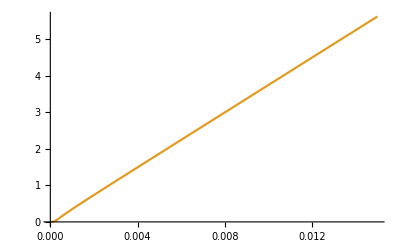

```mathematica
Plot[{X[r],X1[r]},{r,0.00001,0.015},PlotRange->All]
```

```mathematica
X[0.005,L0,r0,P0]
X[0.005,L0,r0]
```

1.53181

X[0.005,0.1,0.006]

```mathematica
Manipulate[Plot[{X[d/2,L0,r0,P0],X1[d/2]},{d,0.0001,0.03},PlotRange->All],{L0,0.0001,0.2},{r0,0.0045,0.1},{P0,8000,12000}]
```

```mathematica
X1[r]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

(2.06471 (-0.0000131947+1.46787×10^-20 √(8.08025×10^29+1.52688×10^44 r^4)))/r

```mathematica
1.3*1.8*0.15/eta
```

19500.

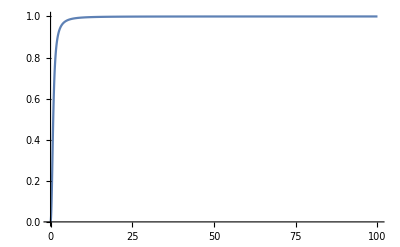

```mathematica
Plot[-1/(2 R^2)+1/2 √((1+4  R^4)/R^4),{R,0,100},PlotRange->All]
```

```mathematica
-1/(2 R^2)+1/2 √((1+4  R^4)/R^4) //Simplify
```

1/2 (√(4+1/R^4)-1/R^2)

```mathematica
XfromU[U_,r_]:= K*2*r/Ux*U
```

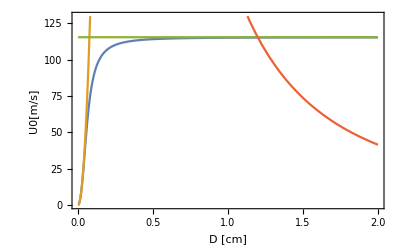

```mathematica
Plot[{U01[d/200],U02[d/200],U03[d/200],U04[d/200]},{d,0.0001,2},PlotRange->{0,130},Frame->True,FrameLabel->{Style["D [cm]",FontSize->14],Style["U0[m/s]",FontSize->14]}]
```

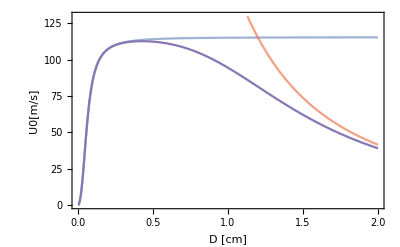

```mathematica
Plot[{U01[d/200],U02[d/200],U03[d/200],U04[d/200],U0[d/200,L0,r0,P0]},{d,0.0001,2},PlotStyle->{{Opacity[0.6]},{Opacity[0.0]},{Opacity[0.0]},{Opacity[0.6]},{Opacity[1]}} ,PlotRange->{0,130},Frame->True,FrameLabel->{Style["D [cm]",FontSize->14],Style["U0[m/s]",FontSize->14]}]
```

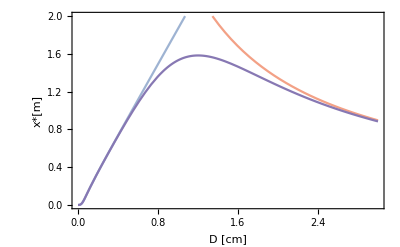

```mathematica
Plot[{XfromU[U01[d/200],d/200],XfromU[U02[d/200],d/200],XfromU[U03[d/200],d/200],XfromU[U04[d/200],d/200],XfromU[U0[d/200,L0,r0,P0],d/200]},{d,0.0001,3},PlotStyle->{{Opacity[0.6]},{Opacity[0.0]},{Opacity[0.0]},{Opacity[0.6]},{Opacity[1]}},PlotRange->{0,2},Frame->True,FrameLabel->{Style["D [cm]",FontSize->14],Style["x*[m]",FontSize->14]}]
```

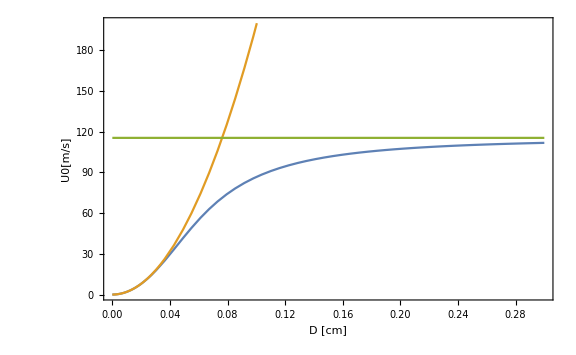

```mathematica
Plot[{U01[r/200],U02[r/200],U03[r/200]},{r,0.00001,0.3},PlotRange->{0,200},Frame->True,FrameLabel->{Style["D [cm]",FontSize->14],Style["U0[m/s]",FontSize->14]}]
```

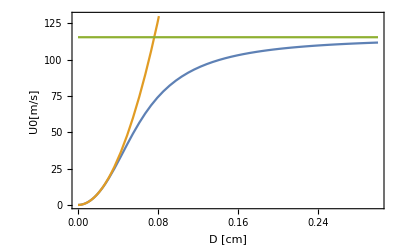

```mathematica
Plot[{U01[d/200],U02[d/200],U03[d/200],U04[d/200]},{d,0.00001,0.3},PlotRange->{0,130},Frame->True,FrameLabel->{Style["D [cm]",FontSize->14],Style["U0[m/s]",FontSize->14]}]
```

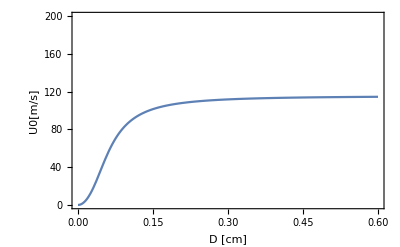

```mathematica
Plot[{U01[d/200]},{d,0.00001,0.6},PlotRange->{0,200},Frame->True,FrameLabel->{Style["D [cm]",FontSize->14],Style["U0[m/s]",FontSize->14]}]
```

```mathematica
ds = {30,25,20,17.5,15,13.5,12,10,8.5,7,5,4,3,2}
```

{30,25,20,17.5,15,13.5,12,10,8.5,7,5,4,3,2}

```mathematica
xs={55,60,82,85,106,123,156,150,130,124,101,66,41,32}
```

{55,60,82,85,106,123,156,150,130,124,101,66,41,32}

```mathematica
errors=xs/50+3
```

{41/10,21/5,116/25,47/10,128/25,273/50,153/25,6,28/5,137/25,251/50,108/25,191/50,91/25}

```mathematica
Phi /.Solve[{deltap[L0/100,r0*1.1,Phi]==(P0),Phi>0},{Phi},Reals][[1]]
```

0.00790072

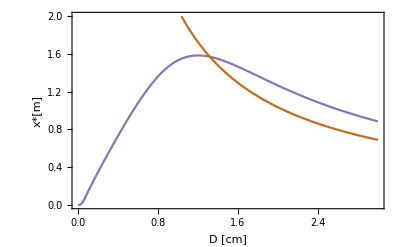

```mathematica
Plot[{XfromU[U01[d/200],d/200],XfromU[U02[d/200],d/200],XfromU[U03[d/200],d/200],XfromU[U04[d/200],d/200],XfromU[U0[d/200,L0,r0,P0],d/200],XfromU[U04[d/200],d/200]/1.3},{d,0.0001,3},PlotStyle->{{Opacity[0]},{Opacity[0.0]},{Opacity[0.0]},{Opacity[0]},{Opacity[1]},{Opacity[1]}},PlotRange->{0,2},Frame->True,FrameLabel->{Style["D [cm]",FontSize->14],Style["x*[m]",FontSize->14]}]
```

```mathematica
data=Transpose[{(ds-0.5)/10,xs/100,errors/100}]
```

{{2.95,11/20,41/1000},{2.45,3/5,21/500},{1.95,41/50,29/625},{1.7,17/20,47/1000},{1.45,53/50,32/625},{1.3,123/100,273/5000},{1.15,39/25,153/2500},{0.95,3/2,3/50},{0.8,13/10,7/125},{0.65,31/25,137/2500},{0.45,101/100,251/5000},{0.35,33/50,27/625},{0.25,41/100,191/5000},{0.15,8/25,91/2500}}

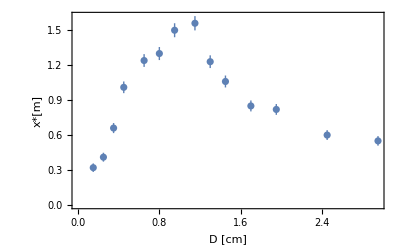

```mathematica
p2=ListPlot[{#1,Around[#2,#3]}&@@@data,Frame->True,FrameLabel->{Style["D [cm]",FontSize->14],Style["x*[m]",FontSize->14]}]
```

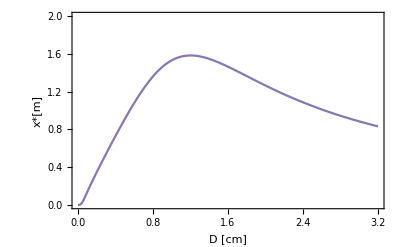

```mathematica
p1=Plot[{XfromU[U01[d/200],d/200],XfromU[U02[d/200],d/200],XfromU[U03[d/200],d/200],XfromU[U04[d/200],d/200],XfromU[U0[d/200,L0,r0,P0],d/200]},{d,0.0001,3.2},PlotStyle->{{Opacity[0.0]},{Opacity[0.0]},{Opacity[0.0]},{Opacity[0.0]},{Opacity[1]}},PlotRange->{0,2},Frame->True,FrameLabel->{Style["D [cm]",FontSize->14],Style["x*[m]",FontSize->14]}]
```

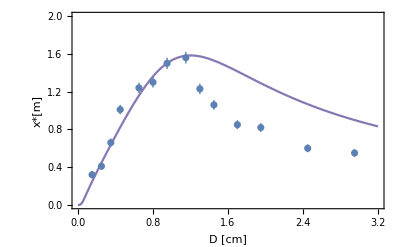

```mathematica
Show[{p1,p2}]
```

```mathematica
Manipulate[Show[{p2,Plot[{X[d/200,L0,r0,P0]},{d,0.0001,3},PlotRange->All]}],{L0,0.0001,0.2},{r0,0.0045,0.0065},{P0,4000,12000}]
```

```mathematica
Manipulate[Show[{p2,Plot[{X[d/200,L0,r0,P0],XfromU[U04[d/200,L0,r0,P0],d/200]/a},{d,0.0001,3},PlotRange->{0,2}]},Frame->True,FrameLabel->{Style["D [cm]",FontSize->14],Style["x*[m]",FontSize->14]}],{L0,0.0001,0.2},{r0,0.005,0.006},{P0,4000,12000},{a,1.3,1.7}]
```

0.07

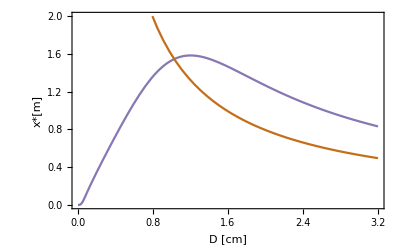

```mathematica
L=0.07
p3=Plot[{XfromU[U01[d/200],d/200],XfromU[U02[d/200],d/200],XfromU[U03[d/200],d/200],XfromU[U04[d/200],d/200],XfromU[U0[d/200,L0,r0,P0],d/200],XfromU[U04[d/200],d/200]*0.59},{d,0.0001,3.2},PlotStyle->{{Opacity[0]},{Opacity[0.0]},{Opacity[0.0]},{Opacity[0]},{Opacity[1]},{Opacity[1]}},PlotRange->{0,2},Frame->True,FrameLabel->{Style["D [cm]",FontSize->14],Style["x*[m]",FontSize->14]}]
```

7

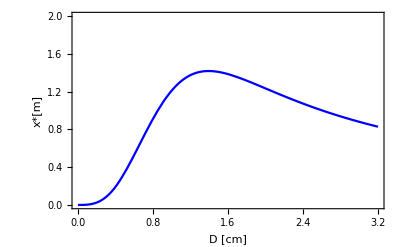

0.07

```mathematica
L=7
p4=Plot[{XfromU[U01[d/200],d/200],XfromU[U02[d/200],d/200],XfromU[U03[d/200],d/200],XfromU[U04[d/200],d/200],XfromU[U0[d/200,L0,r0,P0],d/200],XfromU[U04[d/200],d/200]/1.3},{d,0.0001,3.2},PlotStyle->{{Opacity[0]},{Opacity[0.0]},{Opacity[0.0]},{Opacity[0]},{Opacity[1,Blue]},{Opacity[0]}},PlotRange->{0,2},Frame->True,FrameLabel->{Style["D [cm]",FontSize->14],Style["x*[m]",FontSize->14]}]
L=0.07
```

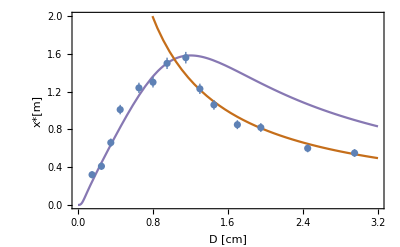

```mathematica
Show[p3,p2]
```

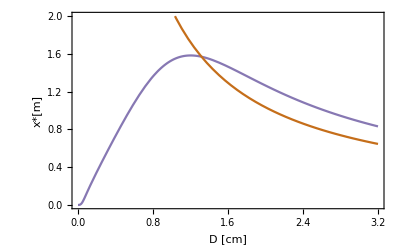

```mathematica
p3
```

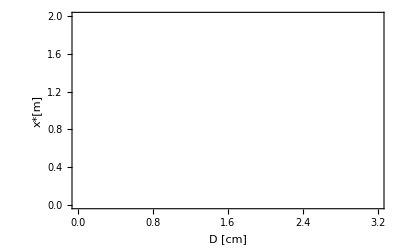

```mathematica
Plot[{XfromU[U0[d/200,L0,r0,P0],d/200]},{d,0.0001,3.2},PlotStyle->{{Opacity[0.0]},{Opacity[0.0]},{Opacity[0.0]},{Opacity[0.0]},{Opacity[1]}},PlotRange->{0,2},Frame->True,FrameLabel->{Style["D [cm]",FontSize->14],Style["x*[m]",FontSize->14]}]
```

```mathematica
U04[3/200,L0,r0,P0]*0.6
```

11.0532